2.62221×10^14

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

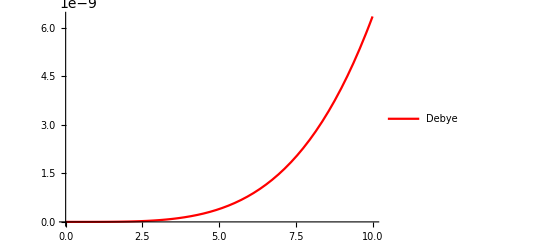

General::munfl: 1.98395×10^14 1.7155318×10^-3209127 is too small to represent as a normalized machine number; precision may be lost.

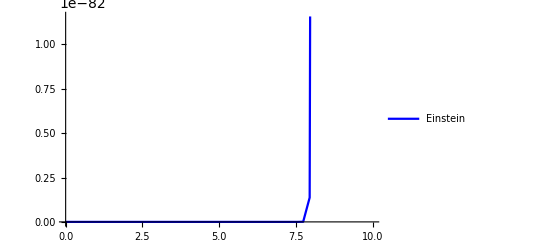

```mathematica
h=1.05*10^-34;(*1.05*10^-34*)
m=4*1.66*10^(-27);(*9.1*10^-31*)
μ0=9*10^4;
ee=1.6*10^(-19);
k=1.38×10^-23;
c=12000;
a=3.57*10^(-10);
n=176.2*10^(27);
wd=(6*π^2*n*c^3)^(1/3)
w0=0.756595wd;
En1[T_]:=9*(k*T)^4/(h*wd)^3*NIntegrate[x^3/(ⅇ^x-1),{x,0, wd*h/(k*T)}]
En2[T_]:=(3*h*w0)/(ⅇ^((h*w0)/(k*T))-1)
a=Plot[En1[T]/(1.6*10^(-19)),{T,0,10}, PlotStyle->Red,PlotLegends->{"Debye"}]
b=Plot[En2[T]/(1.6*10^(-19)),{T,0,10},PlotStyle->Blue,PlotLegends->{"Einstein"}]
```

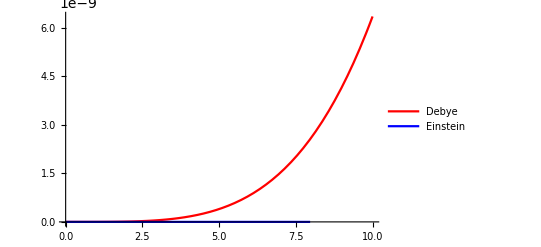

```mathematica
Show[a,b,PlotLegends->{"Debye","Einstein" }]
```

```mathematica
Clear[w0]
```

General::munfl: 1.30185×10^-39 2.2815802547×10^-26717 is too small to represent as a normalized machine number; precision may be lost.

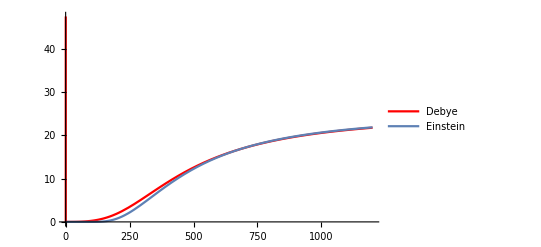

```mathematica
Na=6.02*10^(23);
delta=0.001;
w0=0.756595wd;
Cn1[T_]:=Na*(En1[T+delta]-En1[T-delta])/(2*delta)
Cn2[T_]:=Na*(3*(h*w0)^2*ⅇ^((h*w0)/(k*T)))/(k*T^2*(ⅇ^((h*w0)/(k*T))-1)^2)
a=Plot[Cn1[T],{T,0,1200}, PlotStyle->Red,PlotLegends->{"Debye"}];
b=Plot[Cn2[T],{T,0,1200},PlotLegends->{"Einstein"}];
Show[a,b]
```

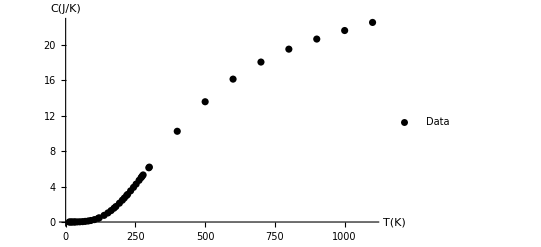

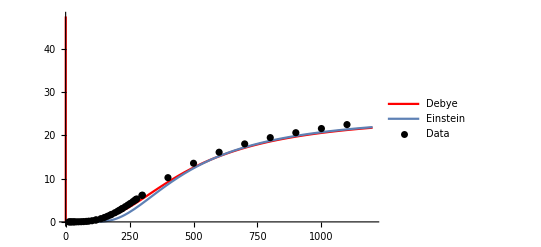

```mathematica
Cdata={{12.833, 0.000115*4.184},
{16.015, 0.000192*4.184},
{21.304, 0.000424*4.184},
{24.100 ,0.000600*4.184},
{31.332 ,0.00135*4.184},
{33.407 ,0.00161*4.184},
{41.319 ,0.00313*4.184},
{50.450 ,0.00579*4.184},
{60.540 ,0.01035*4.184},
{70.070 ,0.01681*4.184},
{80.868 ,0.02762*4.184},
{90.190 ,0.04058*4.184},
{103.085 ,0.06462*4.184},
{116.719 ,0.1009*4.184},
{120.283 ,0.1124*4.184},
{137.805,0.1794*4.184},
{151.444 ,0.2448*4.184},
{162.867 ,0.3083*4.184},
{173.316 ,0.3728*4.184},
{180.042 ,0.4175*4.184},
{192.641 ,0.5072*4.184},
{203.157 ,0.5881*4.184},
{210.341 ,0.6465*4.184},
{218.511 ,0.7146*4.184},
{222.107 ,0.7449*4.184},
{232.816 ,0.8404*4.184},
{243.176 ,0.9341*4.184},
{252.541 ,1.0220*4.184},
{263.168 ,1.1232*4.184},
{270.507 ,1.1967*4.184},
{274.134 ,1.2332*4.184},
{277.675 ,1.2686*4.184},
{298.15, 1.462*4.184},
{300, 1.480*4.184},
{400 ,2.446*4.184},
{500 ,3.242*4.184},
{600 ,3.852*4.184},
{700 ,4.312*4.184},
{800 ,4.660*4.184},
{900 ,4.932*4.184},
{1000 ,5.162*4.184},
{1100 ,5.380*4.184}};
c=ListPlot[Cdata, AxesLabel->{"T(K)", "C(J/K)"},PlotStyle->{Black},PlotLegends->{"Data"}]
Show[a,b,c]
```

```mathematica
Clear[w0]
FindFit[Cdata,Na*(3*(h*w0)^2*ⅇ^((h*w0)/(k*T)))/(k*T^2*(ⅇ^((h*w0)/(k*T))-1)^2),{w0},T]
```

{w0→0.756595}

2.62221×10^14

General::munfl: 2.27423×10^-39 8.4670168623×10^-35321 is too small to represent as a normalized machine number; precision may be lost.

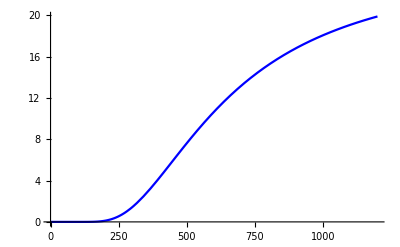

```mathematica
w0=wd
Cn2[T_]:=Na*(3*(h*w0)^2*ⅇ^((h*w0)/(k*T)))/(k*T^2*(ⅇ^((h*w0)/(k*T))-1)^2)
b=Plot[Cn2[T],{T,0,1200},PlotStyle->Blue]
```